# Basic Math Usages:

Basic cmd for math Computing, visualization and presentation.

```mathematica
2+2
```

4

Using = to activate natural language input.

plot a cosine

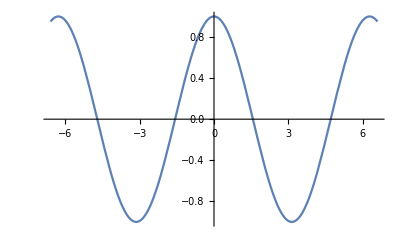

Define function

```mathematica
f[x_] := 3x+3;
f[3]
```

12

Solve Computation

```mathematica
Solve[x^2+5x-6==0,x]
```

{{x→-6},{x→1}}

Use reduce to simplify a set of rules

3<x<5

x<1||2<x<3||x>4

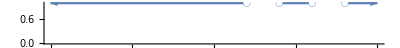

```mathematica
Reduce[ {0<x<5,3<x<8},x]
Reduce[(x-1)(x-2)(x-3)(x-4)>0,x]
NumberLinePlot[%,{x,-5,5}]
```

Plotting

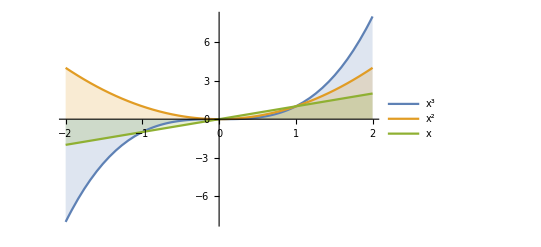

```mathematica
Plot[{x^3, x^2, x}, {x, -2, 2}, PlotLegends -> "Expressions",Filling->Axis]
```

Region Plot

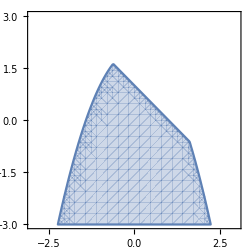

```mathematica
RegionPlot[Reduce[{x^2 + y < 2 && x + y < 1}], {x, -3, 3}, {y, -3, 3}]
```

Combine plots together

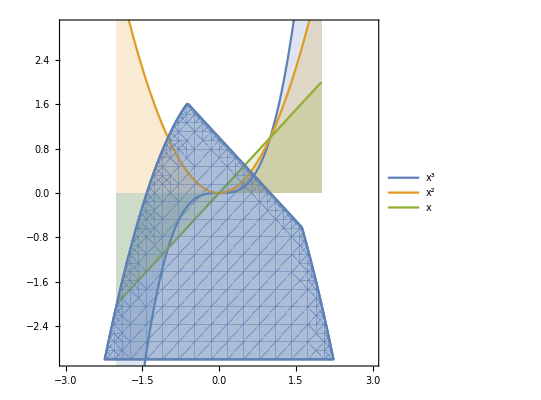

```mathematica
Show[{%,%%}]
```

Combine graphics

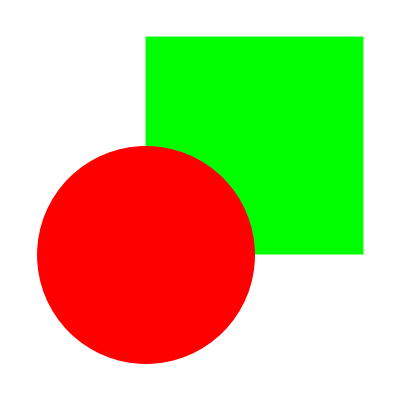

```mathematica
Graphics[{Green, Rectangle[{0, 0}, {2, 2}], Red, Disk[]}]
```

3D object graphics

```mathematica
Graphics3D[Ball[],Axes->True,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

Polar Axis

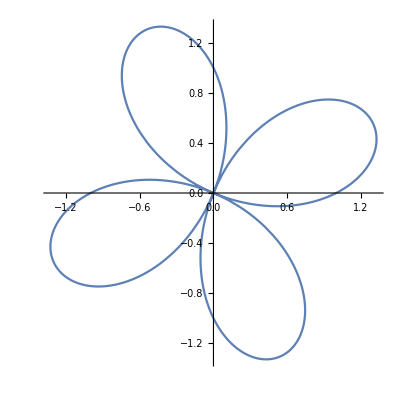

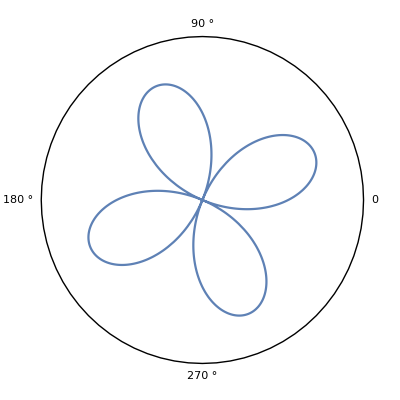

```mathematica
PolarPlot[Sin[2 θ] + Cos[2 θ], {θ, 0, 2 Pi}]
PolarPlot[Sin[2 θ] + Cos[2 θ], {θ, 0, 2 Pi}, 
 PolarAxes -> Automatic, 
 PolarTicks -> {0 °, 90 °, 180 °, 
   270 °}]
```

Recursive array.

```mathematica
RecurrenceTable[{a[x] == 2 a[x - 1], a[1] == 1}, a, {x, 1, 8}]
```

{1,2,4,8,16,32,64,128}

Stat and visualization

```mathematica
RandomVariate[NormalDistribution[0, 1], {500, 2}] // Short
Histogram3D[%]
```

{{0.89314,0.296569},«498»,{0.149505,«19»}}

-Graphics3D-

Interactive Figure

```mathematica
Manipulate[Plot[Sin[f*x + p], {x, -3, 3},
  Filling -> fill,
  PlotStyle -> color],
 {f, 1, 5}, {p, 3, 9}, {fill, {Bottom, Top, Axis}}, {color, Red}]
```